```mathematica
SetDirectory["/Users/dluntzma/Desktop"];
counts2 = Import["20141122_double_slit_bulb_counts2.csv"];
counts2;
```

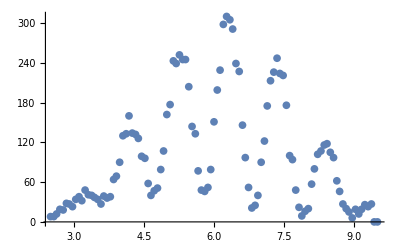

```mathematica
ListPlot[counts2]
```

```mathematica
θ = (x - x0)/R;
α = π * a * Sin[θ]/λ;
β = π * d * Sin[θ]/λ; 

Subscript[i, 2] = Subscript[i, 0] * (Sin[α]/α)^2 * Cos[β]^2;
```

```mathematica
x0= 6.3;
a = 0.090;
d = 0.353;
R = 700;
λ = .000546;
```

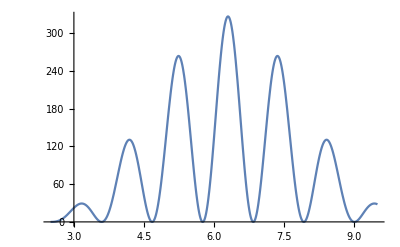

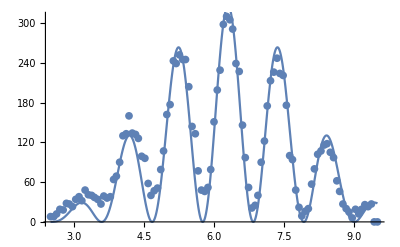

```mathematica
fit2 = NonlinearModelFit[counts2,Subscript[i, 2],{Subscript[i, 0]}, x];
plot2 = Plot[fit2[x], {x, 2.5, 9.5}]
Show[ListPlot[counts2], plot2]
```